# Coca Cola Vs. Pepsi: Fun facts

Yifei Xiao
6/25/2019

People are consuming tons of soda everyday. From Coke to Pepsi, from Sprite to Mountain Dew. Most sparkling beverages we drink today are produced by two companies: Coca-Cola Company and PepsiCo. Both companies have been around for more than 100 years and sell billions of dollars of product annually. The war Pepsi and Coca Cola never ends. This article compares two companies in different aspects and some fun facts.

## 1. Revenue

When talking about a company, the first thing appears in our mind is how much money that company can earn each year. Coca Cola and Pepsi are no exceptions. We first collect raw data from a statistics website “macrotrends”.

```mathematica
ClearAll["Global`*"];
colaRevenueRaw = Import["https://www.macrotrends.net/stocks/charts/KO/coca-cola/revenue", "Data"];
pepsiRevenueRaw=Import["https://www.macrotrends.net/stocks/charts/PEP/pepsico/revenue", "Data"];
```

We are only interested in annual income of two companies, so we need to clean up other unrelated data such as quarterly revenue and so on. The annual income is in the level [[1,3,1,2]], which can be shown in the table form:

```mathematica
colaRevenue = colaRevenueRaw[[1,3,1]]//TableForm
pepsiRevenue = pepsiRevenueRaw[[1,3,1]]//TableForm
```

Coca-Cola Annual Revenue (Millions of US $) |  |  |  |  |  |  |  |  |  |  |  |  | 
2018
$31,856 | 2017
$35,410 | 2016
$41,863 | 2015
$44,294 | 2014
$45,998 | 2013
$46,854 | 2012
$48,017 | 2011
$46,542 | 2010
$35,119 | 2009
$30,990 | 2008
$31,944 | 2007
$28,857 | 2006
$24,088 | 2005
$23,104

Pepsico Annual Revenue (Millions of US $) |  |  |  |  |  |  |  |  |  |  |  |  | 
2018
$64,661 | 2017
$63,525 | 2016
$62,799 | 2015
$63,056 | 2014
$66,683 | 2013
$66,415 | 2012
$65,492 | 2011
$66,504 | 2010
$57,838 | 2009
$43,232 | 2008
$43,251 | 2007
$39,474 | 2006
$35,137 | 2005
$32,562

And we can use line plot to compare them more intuitively:

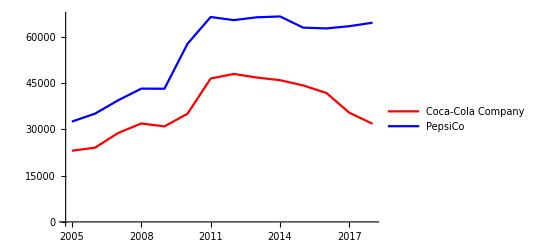

```mathematica
colaRevenue[[1,2,;;,2]]=ToExpression[StringDelete[#,{"$",","}]&/@colaRevenue[[1,2,;;,2]]];
pepsiRevenue[[1,2,;;,2]]=ToExpression[StringDelete[#,{"$",","}]&/@pepsiRevenue[[1,2,;;,2]]];
ListLinePlot[{colaRevenue[[1,2]],pepsiRevenue[[1,2]]},PlotLegends->{"Coca-Cola Company","PepsiCo"},PlotStyle->{Red,Blue}]
```

PepsiCo earns more money than Coca-Cola Company and Coca-Cola company seems never win in this game. However, one thing we should keep in mind is that here we are comparing all products in each company. But when it comes to regular old cola, things change. We select data from “Brandz”, which takes top 100 most valuable global soft drinks brands 2018. Only top 10 beverage brands are selected in this article.

```mathematica
brandDataRaw = Import["https://www.statista.com/statistics/273063/leading-15-most-valuable-global-soft-drink-brands-based-on-brand-value/","Data"];
brandData = brandDataRaw[[2,1,2,1,1,2]][[1;;10]];
brandData[[;;,1]]=StringDelete[#,"*"]&/@brandData[[;;,1]];
brandData[[;;,2]]=ToExpression[StringDelete[#,","]&/@brandData[[;;,2]]];
PieChart[{brandData[[;;,2]]},ChartLabels->{brandData[[;;,1]]}]
```

-Graphics-

As we can see, the brand value of Coca-Cola occupies the vast majority, whereas Pepsi cannot even win Diet Coke(another product by Coca-Cola Company). If we categorize these brands by their companies, we have the following result: